Subject Matter

We acquire a signal of a subject.  Any form of audio/visual will work.

```mathematica
video=Import[NotebookDirectory[]<>"Psychiatric Interviews for Teaching Depression.mp4"];
```

```mathematica
videoframesSelect=Import[NotebookDirectory[]<>"Psychiatric Interviews for Teaching Depression.mov",{"QuickTime","Frames",{1000,1500,3500,5000,10000}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Dataset[FacialFeatures[#,{"Age","Emotion","Image"}]]&/@videoframesSelect
```

{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]}

```mathematica
Overall Entropy
```

Entropy is a measure of information.  The more entropy the less clear the speaker is.  often indicative of something going on with the speaker.

```mathematica
Entropy[video]//N
```

7.53031

```mathematica
Silence vs. Spoken Words
```

Independent of the particular words it is useful to measure tone, cadence and pace of a speaker.  Silence is very useful to measure over repeated interview or journaling sessions.

```mathematica
int=AudioIntervals[video];
```

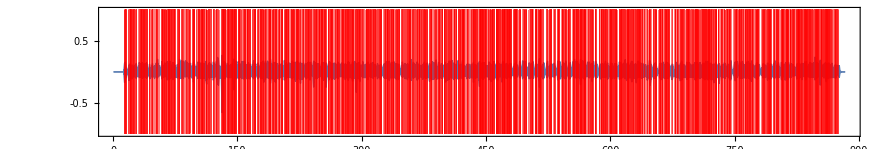

```mathematica
AudioPlot[video,Epilog->{RGBColor[1,0,0,.5],Rectangle[{#[[1]],-1},{#[[2]],1}]&/@int}]
```

```mathematica
Spectral Analysis of Audio
```

This gives us an overall measure of the energy of the speaker.

```mathematica
audiodata=SpectrogramArray[video,2048];
```

```mathematica
MatrixPlot[Transpose[Log@Abs[audiodata]][[1024;;]],AspectRatio->1/3,FrameTicks->None]
```

-Graphics-

```mathematica
Sentiment of Words
```

Understanding the emotional sentiment of words can be useful in understanding a subject, particularly when observed with other facets of the subject over time.  It is useful to see how different topics change sentiment with the subject over time.

```mathematica
(*videoVoice=StringJoin[NetModel["Deep Speech 2 Trained on Baidu English Data"][video]];  Use this to perform Voice to Text if you don't have some other service or CC file*)
```

```mathematica
fullText="- Hello, Alison Wells, do you want to come and have a seat? Hi I’m Dr Taylor one of the GP’s at this surgery, what would you like me to call you? - Alison will be fine - Ok, so what’s brought you here today Alison? - My sister's noticed, I’m just a bit fed up really. My sister said I should come. - Right ok. Has this been going on for some time? - Yeah, few months really. - Ok, do you want to tell me a bit more about what’s been going on? - Just things, things seem to be piling up. - Right - I just don’t seem to be coping with things, - Right - the kids and things. - Right, ok. Would it be OK Alison for me to ask you a few more detailed questions about how you’ve been feeling? - Uhuh - Ok Well if we start with asking you a bit about your mood. How have you been feeling in yourself? - I say a bit fed up. I get up in the morning, everything seems very black. - Right - It’s like, it's just like swimming in, in treacle really and I just don't, I think by tea time when the kids get home, I’ve been having fairly decent conversation with them but... - Right, and can I just check Alison when you say things feel very black, do you feel very miserable? - Fed up, miserable. - Right, OK. And what about sort of feeling tearful? Has that been happening? - I dropped some sugar the other day and I just burst into tears. - Right, OK. - Thanks - So is it the slightest thing that will make you tearful, things that perhaps wouldn’t ordinarily bother you? - Yeah my sister's noticed it as well. - Right, OK. So you’ve been feeling very low with episodes of tearfulness, what about other things, your energy levels are you managing to keep up with things? - I used to do a lot with the kids I used to go swimming, playing but now I just spend the day on the sofa unless I have to go to work. - Right, just remind me, what is it you do for your job? - I work in a supermarket. - Right, so how have you been managing at work? - I’ve not been going in as much cause I just feel so exhausted... ...but I'm just not...the supermarket's been taken over and they’ve cut the wages - Right - and I’ve had problems with the bills - Right - and it's like catalogues just writing me letters, - Uhuh - you know the kids they want all these new games and stuff - Yeah sure - and it’s just y'know. - Things are difficult all round then. With all this going on how are you sleeping Alison? - It just takes me ages to go to sleep, I used to read a book - Right - and just drop off, - Right - but now I just spend my time looking at the clock as it goes round and round. - So from actually getting off to bed and getting off to sleep how long is that taking? - Couple of hours probably. - Right, OK. - Once you’re asleep are you waking up much during the night? - I wake up about...last night I think it was about 4 o clock I woke up. - Right - And can you get back to sleep from that time? - No, no. - And then you’re actually getting out of bed in the morning, are you still feeling tired at that point? - I’m just exhausted, I feel like my brain's not been switched off. I'm just exhausted the next day. - OK - What about eating what’s your appetite been like while you’ve been feeling like this? - I used to have quite a weight problem, but the last couple of months this is a bit looser. - Right - Er, I just... - Do you know how much weight you’ve lost? - No, no. - The kids come in from school and they make their own stuff and I just don’t bother really. - Ok, Ok so you’re appetite's gone down as well. What about things like concentrating and your memory both when you’re watching TV at home or when you’re out doing your job. - How have those things been? - Well I mean pretty useless with the kids, I forgot the swimming money last week, PE kit and parents evening even. - Right, ok. - I just start one job, and, I’m not explaining myself very well. It's like the television, I used to like watching the soaps, EastEnders or something and now 10 minutes later I’m thinking of something else. - Ok, ok. - And what about things Alison you used to enjoy, are there things in life that you still enjoy at the moment? - Nothing really, as I say, a bit useless with the kids. I used to enjoy going out, I used to go out with my friends, the pictures and things, but of course now I can’t be bothered. - Is it that you can’t be bothered and you don’t feel like it as well? - What’s the point really? - Right, ok. - You know. - And I was going to ask, how old are your children now? - I had them a bit later in life, it's took a a long time to have them. I got a girl and a boy, one's 11 and one's 9. - And looking after children takes a lot of time and energy, how are you managing to keep up with that feeling as low as you do? - Well they’re a bit self-sufficient really the kids, they come in from school get their own tea. I should be doing more for them really but I’m not I’m just a bit useless at that at the moment. - Ok, and what about looking after yourself? - Well you can see I’m just a mess. Dave used to say, that’s my boyfriend, - Right - he used to, you know, not have much money but I’d take a bit of pride in what I was doing. My hair and stuff but I can't can't be bothered with that now, there's no point really. - Ok, ok. - And you mentioned Dave, that’s your current partner, how long have you and Dave been together? About a year I met him at work. - And how are things, because often when people feel really down it has an impact on everything including their relationships so how are things with you and Dave at the moment? He’s not ringing as much, he used to text, he’s getting fed up with me not wanting to go out and things. - It’s a slightly embarrassing thing to ask about but I guess it's important, often when people are really feeling very low it affects everything in the relationship including things like their sex life. Have you noticed any changes there for you? He’s always trying to pressure me a little bit - Right - and stuff, but I’m really not into that at the moment. - Right, ok. You just don’t feel like that at the moment. - No. - Ok. So can I just a recap Alison to check I’ve got this right, for the last few months you’ve been feeling really down, no energy, problems with your sleeping and eating, problems with concentrating, not really enjoying things and actually struggling a bit with the kids and perhaps some difficulties in your relationship with Dave. Have I got that right? - Hmmmm. - OK. Can I ask Alison, in the past have there ever been episodes where you’ve felt like this? - When my husband left, I was always crying then for no particular reason. - Right - I haven’t told anybody this before but I took some tablets. - Right So how long ago are we talking was this a few years ago? - About four years ago. - About four years ago. Ok, so you took some tablets, - Yeah - Can you tell me, is it alright to tell me a little bit more about that? - You know what it’s like, the kids are in bed and you’re on your own and I had a few glasses of wine and I just took these tablets. - Right, OK. Can you remember what you actually took at the time what sort of tablets they were? - They were just in the bathroom cabinet, it was paracetamol. - Right, OK. So you took some paracetamol, can you remember roughly how many you took? - About 2 strips, about 12. - Right, OK. - And you’d had a couple of glasses of wine; did you take anything else, any other tablets with it? - No. - Ok. Ok. And was this something Alison that you’d thought about for a while or was it a spur of the moment that evening? - As I say I was crying a lot but I think it was just the wine. - Right, ok. - But you know, I’m just a bit of a burden to everybody really. - And was there any other things that you did around the time, sometimes when people take tablets they leave a note, or do other kinda final acts, get their affairs in order? Did you do any of those things? - No, I just thought, that you know, I'd take the tablets and I'd just go to sleep. - Right, ok. So did you have any thoughts about what taking the tablets would do? Did you.. - I just thought I’d go to sleep and not wake up, but I woke up a couple of hours later and was sick everywhere. - Right, ok. God I was sick. - Ok, so I actually just want to check I get this right because it's important. You actually thought that they would kill you at the time? - I just didn’t want to wake up, - Right, ok - As I say, I’m just useless, I’m a useless mum now and I was then. - Right ok, so you took the tablets and you were very sick in the night did you seek any medical help at the time? - No, no. - Ok. And then were you OK the following day? - Well, yeah, I just felt a bit of a twit really. - Right, did you feel pleased you were still alive? - Yeah, I think you know I realised it was me just being silly. - Right, Ok, Ok. So that was a few years ago, if we just come back to how you are feeling at the moment, you talked about feeling very low… Have there been times currently when you’ve thought about either taking an overdose or doing something else to harm yourself in any way? - You know at night when, when you’re watching the clock and you know, you’re on your own -Yeah - and the kids are in bed. It is, just everything’s so hard, and yeah I suppose, you know, it just feels easy you know? - Right And has that just been something you’ve thought about or have you actually made any plans, got any tablets in or done anything else? - No, no, - Ok - nothing like that. Ok, and I guess it’s a difficult question to ask but one we would ask everybody in your situation. Have things ever been so bad you felt so low that you’ve not only thought about harming yourself or perhaps killing yourself but you’ve also wondered whether the best thing might be to take the children with you? -No, I’d never do anything with my kids I love my kids. No I wouldn’t hurt them. - Ok. - And what about the other side of that, positive things, things to live for... ...things that you feel good about? - Not much at the moment I suppose, kids sometimes you know. They do things that make you think, you know, what’s good about life - Right - and things but... - And are there other things that help at the moment, I’m thinking about people that could be supportive? - My sister as I say she said to get down here and she’s always there, she comes down - Yeah - and rings. I’ve got a couple of friends they’re quite good, - Right - but and Dave when he’s in the mood of course. But I don’t think he’s not going to be around for much longer. - Right. And do you think, or do you feel able to keep yourself safe at the moment from hurting yourself? - I think so yeah, I know I can come here now; you’ve been very good today - Ok. Do you think if that was to change so that you didn’t feel able to keep yourself safe, you’d be able to let anybody know? - All I know is what happened last time that was nothing and I was silly then so I know to come here. - Right, Ok. OK Alison, well thanks for going through all that, I can appreciate it must be very painful. It does sound to me that you are suffering from symptoms that strongly suggest that you are actually depressed at the moment. Now I’m not sure how much you know about depression? - Not much really, not much but I know I just don’t feel right at the moment. - Ok, ok Well I guess just briefly depression can cause a number of problems for people and traditionally we think about people feeling very low and very miserable and often you know thinking about hurting themselves. But it can also affect all other areas of life in terms of problems with eating and sleeping and the other problems you’ve noticed is that concentration and perhaps not really managing as well as normal. I guess the positive side is that you’ve done something about it and you’ve come to talk to me about it today and I think there are almost certainly a range of things we can put in place to help you and treatments that are available. So I guess what I’m thinking is it might be worth us spending a few minutes just thinking about those options for you so that we can start to improve things for you. Would that be alright with you? - I need to do this, yes; I think that’s sensible yeah. - Ok";
```

```mathematica
randomsample=RandomInteger[StringLength[fullText]];StringTake[fullText,{randomsample-100,randomsample}];Classify["Sentiment",StringTake[fullText,{randomsample-100,randomsample}]]
```

Neutral

```mathematica
Movement of Subject in Physical Space
```

A subjects movement in space can be used in-conjunction with other facets to understand a subject.

```mathematica
{w,h}=ImageDimensions[videoframesSelect[[1]]];
res=ImageFeatureTrack[videoframesSelect,Flatten[Table[{x,y},{x,.5,w-.5,20},{y,.5,h-.5,20}],1]];
```

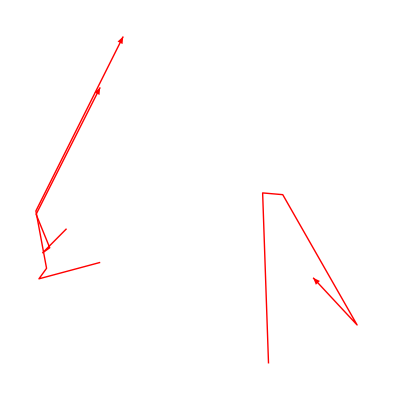

```mathematica
Graphics[{Red,If[FreeQ[#,_Missing],Arrow[{#}]]&/@Transpose[res]}]
```